```mathematica
x[r_,t_] := Log[(1+r^2+2 r Cos[t])/(1+r^2-2 r Cos[t])]
y[r_,t_] := Log[(1+r^2-2 r Sin[t])/(1+r^2+2 r Sin[t])]
z[r_,t_] := 2 ArcTan[2r^2 Sin[2t]/(r^4-1)]
```

```mathematica
v1 = {D[x[r,t],r],D[y[r,t],r],D[z[r,t],r]};
v2 = {D[x[r,t],t],D[y[r,t],t],D[z[r,t],t]};
normal = Simplify[Cross[v1, v2]/Norm[Cross[v1, v2]],1>r> 0&& 2 π>t >=0]
```

{-(2 r Sin[t])/(1+r^2),(2 r Cos[t])/(1+r^2),(-1+r^2)/(1+r^2)}

```mathematica
ParametricPlot3D[{{x[r,t],y[r,t],z[r,t]}},{r,0,1},{t,0,2π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{y[r,t],x[r,t],z[r,t]}},{r,0,1},{t,0,2π}]
```

-Graphics3D-

```mathematica
ContourPlot3D[Sin[2z] == Sinh[x]*Sinh[y],{x,-5,5},{y,-5,5},{z,0, Pi},ContourStyle->White, Mesh->None, Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
ContourPlot3D[Sin[z] == Sinh[x]*Sinh[y],{x,-5,5},{y,-5,5},{z,-Pi/2,3 Pi/2},ContourStyle->White, Mesh->None,BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
scherk =ContourPlot3D[Sin[z] == Sinh[x]*Sinh[y],{x,-30,30},{y,-30,30},{z,-Pi/2,3 Pi/2},ContourStyle->White, Mesh->None,BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
cylinder = ContourPlot3D[x^2+y^2==30^2,{x,-30,30},{y,-30,30},{z,-Pi/2,3 Pi/2},ContourStyle->{Blue,Opacity[0.1]}, Mesh->None,BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
rt1= ContourPlot3D[(x+radius/Cos[τp])^2+(y)^2==(radius Tan[τp])^2,{x,-limit,limit},{y,-limit,limit},{z,-Pi,Pi},ContourStyle->{Black,Opacity[0.5]}, Mesh->None,BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
rt2= ContourPlot3D[(x-radius/Cos[τp])^2+(y)^2==(radius Tan[τp])^2,{x,-limit,limit},{y,-limit,limit},{z,-Pi,Pi},ContourStyle->{Black,Opacity[0.5]}, Mesh->None,BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
Show[cylinder,scherk,rt1,rt2,Boxed->False,Axes->None]
```

-Graphics3D-

```mathematica
FullSimplify[Sin[z[r,t]] - Sinh[x[r,t]]*Sinh[y[r,t]]] /.{r->0.5, t-> 0.1}
```

0.488976

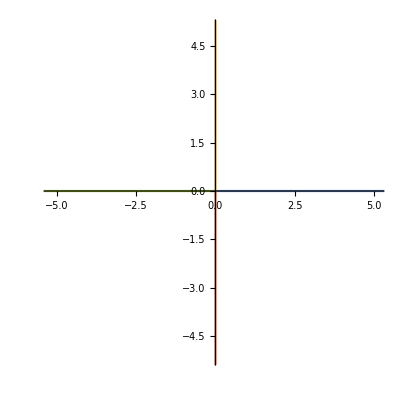

```mathematica
ParametricPlot[{{x[r,0],y[r,0]},{x[r,3π/2],y[r,3π/2]},{x[r,π],y[r,π]},{x[r,π/2],y[r,π/2]}},{r,0,1}]
```

```mathematica
FullSimplify[Sinh[x[r,t]]*Sinh[y[r,t]]]
```

-(8 (r+r^3)^2 Sin[2 t])/(1+r^8-2 r^4 Cos[4 t])

```mathematica
Sin[z[r,t]/2] //FullSimplify
```

(2 r^2 Sin[2 t])/((-1+r^4) √(1+(4 r^4 Sin[2 t]^2)/((-1+r^4)^2)))

```mathematica
Cos[z[r,t]/2]
```

1/(√(1+(4 r^4 Sin[2 t]^2)/((-1+r^4)^2)))

```mathematica
FullSimplify[2Sin[z[r,t]/2]Cos[z[r,t]/2]]
```

(4 r^2 (-1+r^4) Sin[2 t])/(1+r^8-2 r^4 Cos[4 t])

```mathematica
FullSimplify[1-2Sin[z[r,t]/2]^2]
```

-1+(2 (-1+r^4)^2)/(1+r^8-2 r^4 Cos[4 t])

```mathematica
2FullSimplify[ComplexExpand[Re[Log[(1+r Exp[ⅈ t] )]-Log[(1-r Exp[ⅈ t])]]], {0<r<1, 0<= t <2π}]
```

Log[(1+r^2+2 r Cos[t])/(1+r^2-2 r Cos[t])]

```mathematica
2Simplify[ComplexExpand[Re[2 ⅈ ArcTan[r Exp[ⅈ t]]]], {0<r<1, 0<= t <2π}]
```

Log[(1+r^2-2 r Sin[t])/(1+r^2+2 r Sin[t])]

```mathematica
Tan[Simplify[ComplexExpand[Re[ⅈ(Log[(1+r^2 Exp[2 ⅈ t] )]-Log[(1-r^2 Exp[2ⅈ t])])]], {0<r<1, 0<= t <2π}]]/2
```

1/2 Tan[Arg[1-ⅇ^(2 ⅈ t) r^2]-Arg[1+ⅇ^(2 ⅈ t) r^2]]

```mathematica
N[x[1,3π/4]]
N[y[1,3π/4]]
```

-1.76275

-1.76275

```mathematica
τ = Pi/4;
x[r_,t_] := Cos[τ]Log[(1+r^2+2 r Cos[t -τ])/(1+r^2-2 r Cos[t-τ])] + 2 Sin[τ] ArcTan[2 r Sin[t-τ]/(1-r^2)]
y[r_,t_] := Log[(1+r^2-2 r Sin[t])/(1+r^2+2 r Sin[t])] - Tan[τ] ArcTan[-2r Cos[τ]/(1-r^2)] +2 Sin[τ]Log[(1+r^2+2 r Cos[t -τ])/(1+r^2-2 r Cos[t-τ])] + 2 Sin[τ]Tan[τ]ArcTan[2 r Sin[t-τ]/(1-r^2)]
z[r_,t_] := 2 ArcTan[(r^2 (Sin[2(t-τ)] + Sin[2 t])-Sin[2τ])/(r^4-Cos[2τ])] - 4τ + 0.5 Tan[τ]Log[(1+r^4+2 r ^2Cos[2 t ])/(1+r^4-2 r^2 Cos[2t-2 τ])]
```

```mathematica
ParametricPlot3D[{{x[r,t],y[r,t],z[r,t]}},{r,0,1},{t,0,2π}]
```

-Graphics3D-

```mathematica
Quit
```

```mathematica
Clear["Global`*"]
```

```mathematica
τ = Pi/8;
τp = ArcCos[30/radius];
x[r_,t_] := (1/(16 Cos[τ]))(Log[(1+r^2+2 r Cos[t -τ])/(1+r^2-2 r Cos[t-τ])]  + Log[(1+r^2+2 r Cos[t +τ])/(1+r^2-2 r Cos[t+τ])] )
y[r_,t_] := (1/(16 Sin[τ]))(-Log[(1+r^2+2 r Cos[t -τ])/(1+r^2-2 r Cos[t-τ])]  + Log[(1+r^2+2 r Cos[t +τ])/(1+r^2-2 r Cos[t+τ])] )
v[r_,t_] := (1/(8 Sin[τ]Cos[τ]))(ArcTan[(Sin[4τ] + r^2 Sin[2(t-τ)]-r^2Sin[2(t+τ)])/(r^4 + Cos[4 τ]-r^2 Cos[2(t-τ)]-r^2 Cos[2(t+τ)])]-4τ)
```

```mathematica
v[r,t]
```

1/8 (-4 τ+ArcTan[(r^2 Sin[2 (t-τ)]+Sin[4 τ]-r^2 Sin[2 (t+τ)])/(r^4-r^2 Cos[2 (t-τ)]+Cos[4 τ]-r^2 Cos[2 (t+τ)])]) Csc[τ] Sec[τ]

```mathematica
ParametricPlot3D[{{x[r,t],y[r,t],z[r,t]}},{r,0,1},{t,0,2π}]
```

-Graphics3D-

```mathematica
NSolve[Cos[z] == Cos[τ]^2 Cosh[x/Cos[τ]]- Sin[τ]^2 Cosh[y/Sin[τ]] /. {z->0, x->30},y]
```

{{y→ConditionalExpression[0.382683 (-34.2345+(0.+6.28319 ⅈ) C[1]), C[1]∈ℤ]},{y→ConditionalExpression[0.382683 (34.2345+(0.+6.28319 ⅈ) C[1]), C[1]∈ℤ]}}

```mathematica
Out[51] /. C[1]->0
```

{{y→-13.101+0. ⅈ},{y→13.101+0. ⅈ}}

```mathematica
Sqrt[13.100981010145986^2 + 30^2]
```

32.7358

```mathematica
30/Cos[τ]
```

30 Sec[π/8]

```mathematica
N[30 Sec[π/8]]
```

32.4718

```mathematica
τ=Pi/8;
```

```mathematica
limit = 30;
```

```mathematica
Style[x^2+y^2,Hue[0.01]]
```

x^2+y^2

```mathematica
ColorConvert[RGBColor[252,89,89], "HSB"] //InputForm
```

Hue[0., 0., 1.]

```mathematica
scherk = ContourPlot3D[Cos[z] == Cos[τ]^2 Cosh[x/Cos[τ]]- Sin[τ]^2 Cosh[y/Sin[τ]],{x,-limit,limit},{y,-limit,limit},{z,-Pi, Pi},ColorFunction->Function[{x},Hue[(x)/30,96,67]], Mesh->None,BoxRatios->Automatic]
```

```mathematica
radius = 32.73584737605253;
```

```mathematica
cylinder1 = ContourPlot3D[x^2+y^2==(radius)^2,{x,-radius,radius},{y,-13.100981010145986,13.100981010145986},{z,-Pi, Pi},ContourStyle->{Black,Opacity[0.1]}, Mesh->None,BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
cylinder2 = ContourPlot3D[x^2+y^2==(radius)^2,{x,-radius,radius},{y,13.100981010145986,radius},{z,-Pi, Pi},ContourStyle->{Black,Opacity[0.8]}, Mesh->None,BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
cylinder3 = ContourPlot3D[x^2+y^2==(radius)^2,{x,-radius,radius},{y,-13.100981010145986,-radius},{z,-Pi, Pi},ContourStyle->{Black,Opacity[0.8]}, Mesh->None,BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
Show[scherk, cylinder1,cylinder2,cylinder3, rt1, rt2, PlotRange->All,Boxed->False,Axes->None]
```

-Graphics3D-

```mathematica
x[r,t]
y[r,t]
z[r,t]
```

1/16 (Log[(1+r^2+2 r Cos[π/8-t])/(1+r^2-2 r Cos[π/8-t])]+Log[(1+r^2+2 r Cos[π/8+t])/(1+r^2-2 r Cos[π/8+t])]) Sec[π/8]

1/16 Csc[π/8] (-Log[(1+r^2+2 r Cos[π/8-t])/(1+r^2-2 r Cos[π/8-t])]+Log[(1+r^2+2 r Cos[π/8+t])/(1+r^2-2 r Cos[π/8+t])])

1/8 (-π/2+ArcTan[(1+r^2 Sin[2 (-π/8+t)]-r^2 Sin[2 (π/8+t)])/(r^4-r^2 Cos[2 (-π/8+t)]-r^2 Cos[2 (π/8+t)])]) Csc[π/8] Sec[π/8]

```mathematica
y[0.5, Pi/4]
 x[0.5, Pi/4]
z[0.5,Pi/4]
```

-0.207969

0.160362

-0.0293668

```mathematica
f[r_,θ_]:={{1/2 Re[(ⅇ^(ⅈ ϕ) (ArcTanh[ⅇ^(ⅈ (θ-ϕ)) r]+ArcTanh[ⅇ^(ⅈ (θ+ϕ)) r]))/(1+ⅇ^(2 ⅈ ϕ))]},{1/2 Im[(ⅇ^(ⅈ ϕ) (ArcTanh[ⅇ^(ⅈ (θ-ϕ)) r]-ArcTanh[ⅇ^(ⅈ (θ+ϕ)) r]))/(-1+ⅇ^(2 ⅈ ϕ))]},{1/4 Im[Csc[2 ϕ] Log[(ⅇ^(4 ⅈ ϕ)-ⅇ^(2 ⅈ (θ+ϕ)) r^2)/(-1+ⅇ^(2 ⅈ (θ+ϕ)) r^2)]]}}
```

```mathematica
ParametricPlot3D[{f[r, θ],{{1/2 Re[(ⅇ^(ⅈ ϕ) (ArcTanh[ⅇ^(ⅈ (θ-ϕ)) r]+ArcTanh[ⅇ^(ⅈ (θ+ϕ)) r]))/(1+ⅇ^(2 ⅈ ϕ))]},{1/2 Im[(ⅇ^(ⅈ ϕ) (ArcTanh[ⅇ^(ⅈ (θ-ϕ)) r]-ArcTanh[ⅇ^(ⅈ (θ+ϕ)) r]))/(-1+ⅇ^(2 ⅈ ϕ))]},{-5Pi/4+Pi/8-1/4 Im[Csc[2 ϕ] Log[(ⅇ^(4 ⅈ ϕ)-ⅇ^(2 ⅈ (θ+ϕ)) r^2)/(-1+ⅇ^(2 ⅈ (θ+ϕ)) r^2)]]}}} /. ϕ->Pi/16,{r,0,1},{θ,0,2π}, AspectRatio->1]
```

-Graphics3D-

```mathematica
?ParametricPlot3D
```

```mathematica
z1 = E^{I ϕ1};
z2 = E^{I ϕ2};
genericF[z_] := {{1/2 Re[(-(z2-z1^2 z2) ArcTan[z/z1]-z1 (-1+z2^2) ArcTanh[z/z2])/(z1 (z1-z2) z2 (z1+z2))]},1/2 Re[I (-((1+z1^2) z2 ArcTanh[z/z1])+z1 (1+z2^2) ArcTanh[z/z2])/(z1 z2 (z1^2-z2^2))], Re[Log[(z2^2 z^2-z2^2 z1^2)/(z1^2 z^2-z1^2 z2^2)]/(2 (z1^2-z2^2))]}
```

```mathematica
genericF[r E^{I θ}]
```

{{{1/2 Re[(ⅇ^(-ⅈ ϕ1-ⅈ ϕ2) ((ⅇ^(2 ⅈ ϕ1+ⅈ ϕ2)-ⅇ^(ⅈ ϕ2)) ArcTan[ⅇ^(ⅈ θ-ⅈ ϕ1) r]-ⅇ^(ⅈ ϕ1) (-1+ⅇ^(2 ⅈ ϕ2)) ArcTanh[ⅇ^(ⅈ θ-ⅈ ϕ2) r]))/((ⅇ^(ⅈ ϕ1)-ⅇ^(ⅈ ϕ2)) (ⅇ^(ⅈ ϕ1)+ⅇ^(ⅈ ϕ2)))]}},{-1/2 Im[(ⅇ^(-ⅈ ϕ1-ⅈ ϕ2) (-ⅇ^(ⅈ ϕ2) (1+ⅇ^(2 ⅈ ϕ1)) ArcTanh[ⅇ^(ⅈ θ-ⅈ ϕ1) r]+ⅇ^(ⅈ ϕ1) (1+ⅇ^(2 ⅈ ϕ2)) ArcTanh[ⅇ^(ⅈ θ-ⅈ ϕ2) r]))/(ⅇ^(2 ⅈ ϕ1)-ⅇ^(2 ⅈ ϕ2))]},{1/2 Re[Log[(-ⅇ^(2 ⅈ ϕ1+2 ⅈ ϕ2)+ⅇ^(2 ⅈ θ+2 ⅈ ϕ2) r^2)/(-ⅇ^(2 ⅈ ϕ1+2 ⅈ ϕ2)+ⅇ^(2 ⅈ θ+2 ⅈ ϕ1) r^2)]/(ⅇ^(2 ⅈ ϕ1)-ⅇ^(2 ⅈ ϕ2))]}}

```mathematica
ParametricPlot3D[genericF[r E^{I θ}] /. {ϕ1->Pi/8, ϕ2->-Pi/16},{r,0,1},{θ,0,2π}, AspectRatio->1]
```

-Graphics3D-